```mathematica
data=Import["C:\\Users\\abduld\\Downloads\\Analytics All Web Site Data Location 20121201-20130223 (1).csv"][[8;;-3,;;2]];
```

```mathematica
data=Table[elem[[1]]->{elem[[2]],WolframAlpha[elem[[1]],{{"Input",1},"Input"},PodStates->{"Identifiers:CountryData__More"}]/.HoldComplete[CountryData[x_]]:>x},{elem,data}];
```

```mathematica
m=Max[data[[All,2,1]]];
```

```mathematica
data
```

```mathematica
data={"United States"->{41924,"UnitedStates"},"India"->{9433,"India"},"Russia"->{9013,"Russia"},"Spain"->{7146,"Spain"},"Canada"->{4917,"Canada"},"United Kingdom"->{4802,"UnitedKingdom"},"Germany"->{4579,"Germany"},"Ukraine"->{3730,"Ukraine"},"Brazil"->{3585,"Brazil"},"China"->{3210,"China"},"France"->{3172,"France"},"Italy"->{2537,"Italy"},"(not set)"->{2502,Missing["NotAvailable"]},"Poland"->{2488,"Poland"},"Greece"->{2232,"Greece"},"Australia"->{2227,"Australia"},"Netherlands"->{1921,"Netherlands"},"Sweden"->{1819,"Sweden"},"Romania"->{1790,"Romania"},"Portugal"->{1606,"Portugal"},"Colombia"->{1561,"Colombia"},"Switzerland"->{1555,"Switzerland"},"Mexico"->{1427,"Mexico"},"Singapore"->{1407,"Singapore"},"Israel"->{1312,"Israel"},"Ireland"->{1244,"Ireland"},"Finland"->{1190,"Finland"},"Japan"->{1138,"Japan"},"Taiwan"->{1125,"Taiwan"},"Serbia"->{1118,"Serbia"},"Belarus"->{1051,"Belarus"},"Egypt"->{994,"Egypt"},"Croatia"->{993,"Croatia"},"Norway"->{980,"Norway"},"Czech Republic"->{891,"CzechRepublic"},"Argentina"->{807,"Argentina"},"South Korea"->{803,"SouthKorea"},"Hungary"->{778,"Hungary"},"Pakistan"->{775,"Pakistan"},"Hong Kong"->{758,"HongKong"},"Turkey"->{740,"Turkey"},"Iran"->{687,"Iran"},"Belgium"->{666,"Belgium"},"Saudi Arabia"->{634,"SaudiArabia"},"Denmark"->{576,"Denmark"},"Peru"->{576,"Peru"},"Vietnam"->{533,"Vietnam"},"Austria"->{514,"Austria"},"South Africa"->{467,"SouthAfrica"},"New Zealand"->{453,"NewZealand"},"Malaysia"->{443,"Malaysia"},"Indonesia"->{433,"Indonesia"},"Slovenia"->{424,"Slovenia"},"Sri Lanka"->{410,"SriLanka"},"Thailand"->{384,"Thailand"},"Bulgaria"->{349,"Bulgaria"},"Latvia"->{347,"Latvia"},"Venezuela"->{321,"Venezuela"},"Kazakhstan"->{285,"Kazakhstan"},"Lithuania"->{276,"Lithuania"},"Slovakia"->{254,"Slovakia"},"Estonia"->{252,"Estonia"},"Costa Rica"->{247,"CostaRica"},"Ecuador"->{226,"Ecuador"},"Chile"->{193,"Chile"},"Algeria"->{174,"Algeria"},"Moldova"->{161,"Moldova"},"Cameroon"->{160,"Cameroon"},"Luxembourg"->{150,"Luxembourg"},"Philippines"->{144,"Philippines"},"Armenia"->{139,"Armenia"},"Bangladesh"->{137,"Bangladesh"},"Macedonia [FYROM]"->{121,"Macedonia"},"Tunisia"->{108,"Tunisia"},"Dominican Republic"->{101,"DominicanRepublic"},"Bosnia and Herzegovina"->{96,"BosniaHerzegovina"},"Honduras"->{92,"Honduras"},"Ethiopia"->{86,"Ethiopia"},"Cyprus"->{84,"Cyprus"},"Uruguay"->{84,"Uruguay"},"United Arab Emirates"->{81,"UnitedArabEmirates"},"Nepal"->{68,"Nepal"},"Morocco"->{66,"Morocco"},"Puerto Rico"->{58,"PuertoRico"},"Bolivia"->{56,"Bolivia"},"Paraguay"->{55,"Paraguay"},"Madagascar"->{52,"Madagascar"},"Uzbekistan"->{47,"Uzbekistan"},"Trinidad and Tobago"->{43,"TrinidadTobago"},"Nigeria"->{41,"Nigeria"},"Kuwait"->{40,"Kuwait"},"Cuba"->{39,"Cuba"},"Uganda"->{39,"Uganda"},"SÃ£o TomÃ© and PrÃncipe"->{38,Missing["NotAvailable"]},"Kenya"->{31,"Kenya"},"Mauritius"->{27,"Mauritius"},"Nicaragua"->{24,"Nicaragua"},"Mongolia"->{22,"Mongolia"},"Iceland"->{21,"Iceland"},"Qatar"->{21,"Qatar"},"Angola"->{19,"Angola"},"Jordan"->{19,"Jordan"},"El Salvador"->{16,"ElSalvador"},"Lebanon"->{15,"Lebanon"},"Brunei"->{14,"Brunei"},"Barbados"->{13,"Barbados"},"Bahrain"->{13,"Bahrain"},"Botswana"->{13,"Botswana"},"Macau"->{12,"Macau"},"Senegal"->{11,"Senegal"},"Guatemala"->{9,"Guatemala"},"Myanmar [Burma]"->{9,"Myanmar"},"Andorra"->{8,"Andorra"},"Albania"->{6,"Albania"},"Jamaica"->{6,"Jamaica"},"Tanzania"->{6,"Tanzania"},"Georgia"->{5,Missing["NotAvailable"]},"Saint Lucia"->{5,"SaintLucia"},"Monaco"->{5,"Monaco"},"Oman"->{5,"Oman"},"Fiji"->{4,"Fiji"},"Faroe Islands"->{4,"FaroeIslands"},"Ghana"->{4,"Ghana"},"Aruba"->{3,"Aruba"},"CÃ.b4te dâ.80.99Ivoire"->{3,Missing["NotAvailable"]},"Maldives"->{3,"Maldives"},"Palestinian Territories"->{3,"PalestinianTerritories"},"Togo"->{3,"Togo"},"Guernsey"->{2,"Guernsey"},"Jersey"->{2,"Jersey"},"Montenegro"->{2,"Montenegro"},"Rwanda"->{2,"Rwanda"},"Syria"->{2,"Syria"},"Zambia"->{2,"Zambia"},"Azerbaijan"->{1,"Azerbaijan"},"Belize"->{1,"Belize"},"Congo [DRC]"->{1,"DemocraticRepublicCongo"},"Kyrgyzstan"->{1,"Kyrgyzstan"},"Cayman Islands"->{1,"CaymanIslands"},"Namibia"->{1,"Namibia"},"Panama"->{1,"Panama"},"Seychelles"->{1,"Seychelles"},"Sudan"->{1,"Sudan"},"Yemen"->{1,"Yemen"}};
```

```mathematica
cs=Table[{
LightBlue,
Tooltip[CountryData[First[elem],"Polygon"],elem[[2,1]]]/.CountryData[___]:> {},
},{elem,data}];
```

CountryData::notent: "___" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData::notent: "\"(not set)\"" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData::notent: "\"Macedonia [FYROM]\"" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

General::stop: Further output of CountryData :: notent will be suppressed during this calculation.

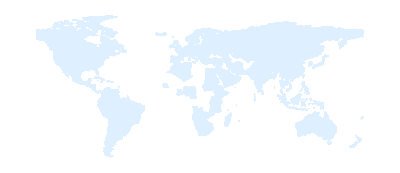

```mathematica
Graphics[cs]
```

```mathematica
Select[Table[elem[[2,1]]/CountryData[First[elem],"Population"],{elem,data}],NumberQ]//Max
```

CountryData::notent: "\"(not set)\"" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData::notent: "\"Macedonia [FYROM]\"" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

CountryData::notent: "\"S\[CapitalATilde]\[Sterling]o Tom\[CapitalATilde]\[Copyright] and Pr\[CapitalATilde]\[DiscretionaryHyphen]ncipe\"" is not a known entity, class, or tag for CountryData. Use CountryData[] for a list of entities.

General::stop: Further output of CountryData :: notent will be suppressed during this calculation.

0.000304878

```mathematica
1/0.0003048780487804878
```

3280.

```mathematica
With[{mult=10000},
Graphics[{
{
EdgeForm[Black],
FaceForm[],
CountryData[#,"Polygon"]&/@CountryData[]
},
Quiet[
Select[
Table[{
EdgeForm[Black],
ColorData["DarkRainbow"][mult*elem[[2,1]]/CountryData[First[elem],"Population"]],
Tooltip[CountryData[First[elem],"Polygon"]/.CountryData[___]->{},mult*elem[[2,1]]/CountryData[First[elem],"Population"]],
If[CountryData[First[elem],"Area"]>2000000,
{
Black,
Inset[Round[mult*elem[[2,1]]/CountryData[First[elem],"Population"],0.01],Reverse@CountryData[First[elem],"CenterCoordinates"]]
}
]
},{elem,data}],MatchQ[#,{_,_RGBColor,___,_Tooltip,___}]&]
]
}]
]
```

-Graphics-

```mathematica
With[{mult=100000000},
Graphics[{
{
EdgeForm[Black],
FaceForm[],
CountryData[#,"Polygon"]&/@CountryData[]
},
Quiet[
Select[
Table[{
EdgeForm[Black],
ColorData["DarkRainbow"][mult*elem[[2,1]]/CountryData[First[elem],"GDP"]],
Tooltip[CountryData[First[elem],"Polygon"]/.CountryData[___]->{},mult*elem[[2,1]]/CountryData[First[elem],"GDP"]],
If[CountryData[First[elem],"Area"]>2000000,
{
Black,
Inset[Round[mult*elem[[2,1]]/CountryData[First[elem],"GDP"],0.1],Reverse@CountryData[First[elem],"CenterCoordinates"]]
}
]
},{elem,data}],MatchQ[#,{_,_RGBColor,___,_Tooltip,___}]&]
]
}]
]
```

-Graphics-

```mathematica
Graphics`Mesh`MeshInit[]

usa=CountryData["USA","Coordinates"]/.{a_,b_}:>{a,b,0.0};

GeometryPlot3D[Polygon[usa],Axes->True,Extrusion->{3.0,0.0},ExtrusionStyle->Green]
```

{Utilities`URLTools`,JLink`,WolframAlphaClient`,PacletManager`,WebServices`,System`,Global`,Graphics`Mesh`}

-Graphics3D-

```mathematica
countries={"United States"->{41924,"UnitedStates"},"India"->{9433,"India"},"Russia"->{9013,"Russia"},"Spain"->{7146,"Spain"},"Canada"->{4917,"Canada"},"United Kingdom"->{4802,"UnitedKingdom"},"Germany"->{4579,"Germany"},"Ukraine"->{3730,"Ukraine"},"Brazil"->{3585,"Brazil"},"China"->{3210,"China"},"France"->{3172,"France"},"Italy"->{2537,"Italy"},"(not set)"->{2502,Missing["NotAvailable"]},"Poland"->{2488,"Poland"},"Greece"->{2232,"Greece"},"Australia"->{2227,"Australia"},"Netherlands"->{1921,"Netherlands"},"Sweden"->{1819,"Sweden"},"Romania"->{1790,"Romania"},"Portugal"->{1606,"Portugal"},"Colombia"->{1561,"Colombia"},"Switzerland"->{1555,"Switzerland"},"Mexico"->{1427,"Mexico"},"Singapore"->{1407,"Singapore"},"Israel"->{1312,"Israel"},"Ireland"->{1244,"Ireland"},"Finland"->{1190,"Finland"},"Japan"->{1138,"Japan"},"Taiwan"->{1125,"Taiwan"},"Serbia"->{1118,"Serbia"},"Belarus"->{1051,"Belarus"},"Egypt"->{994,"Egypt"},"Croatia"->{993,"Croatia"},"Norway"->{980,"Norway"},"Czech Republic"->{891,"CzechRepublic"},"Argentina"->{807,"Argentina"},"South Korea"->{803,"SouthKorea"},"Hungary"->{778,"Hungary"},"Pakistan"->{775,"Pakistan"},"Hong Kong"->{758,"HongKong"},"Turkey"->{740,"Turkey"},"Iran"->{687,"Iran"},"Belgium"->{666,"Belgium"},"Saudi Arabia"->{634,"SaudiArabia"},"Denmark"->{576,"Denmark"},"Peru"->{576,"Peru"},"Vietnam"->{533,"Vietnam"},"Austria"->{514,"Austria"},"South Africa"->{467,"SouthAfrica"},"New Zealand"->{453,"NewZealand"},"Malaysia"->{443,"Malaysia"},"Indonesia"->{433,"Indonesia"},"Slovenia"->{424,"Slovenia"},"Sri Lanka"->{410,"SriLanka"},"Thailand"->{384,"Thailand"},"Bulgaria"->{349,"Bulgaria"},"Latvia"->{347,"Latvia"},"Venezuela"->{321,"Venezuela"},"Kazakhstan"->{285,"Kazakhstan"},"Lithuania"->{276,"Lithuania"},"Slovakia"->{254,"Slovakia"},"Estonia"->{252,"Estonia"},"Costa Rica"->{247,"CostaRica"},"Ecuador"->{226,"Ecuador"},"Chile"->{193,"Chile"},"Algeria"->{174,"Algeria"},"Moldova"->{161,"Moldova"},"Cameroon"->{160,"Cameroon"},"Luxembourg"->{150,"Luxembourg"},"Philippines"->{144,"Philippines"},"Armenia"->{139,"Armenia"},"Bangladesh"->{137,"Bangladesh"},"Macedonia [FYROM]"->{121,"Macedonia"},"Tunisia"->{108,"Tunisia"},"Dominican Republic"->{101,"DominicanRepublic"},"Bosnia and Herzegovina"->{96,"BosniaHerzegovina"},"Honduras"->{92,"Honduras"},"Ethiopia"->{86,"Ethiopia"},"Cyprus"->{84,"Cyprus"},"Uruguay"->{84,"Uruguay"},"United Arab Emirates"->{81,"UnitedArabEmirates"},"Nepal"->{68,"Nepal"},"Morocco"->{66,"Morocco"},"Puerto Rico"->{58,"PuertoRico"},"Bolivia"->{56,"Bolivia"},"Paraguay"->{55,"Paraguay"},"Madagascar"->{52,"Madagascar"},"Uzbekistan"->{47,"Uzbekistan"},"Trinidad and Tobago"->{43,"TrinidadTobago"},"Nigeria"->{41,"Nigeria"},"Kuwait"->{40,"Kuwait"},"Cuba"->{39,"Cuba"},"Uganda"->{39,"Uganda"},"SÃ£o TomÃ© and PrÃncipe"->{38,Missing["NotAvailable"]},"Kenya"->{31,"Kenya"},"Mauritius"->{27,"Mauritius"},"Nicaragua"->{24,"Nicaragua"},"Mongolia"->{22,"Mongolia"},"Iceland"->{21,"Iceland"},"Qatar"->{21,"Qatar"},"Angola"->{19,"Angola"},"Jordan"->{19,"Jordan"},"El Salvador"->{16,"ElSalvador"},"Lebanon"->{15,"Lebanon"},"Brunei"->{14,"Brunei"},"Barbados"->{13,"Barbados"},"Bahrain"->{13,"Bahrain"},"Botswana"->{13,"Botswana"},"Macau"->{12,"Macau"},"Senegal"->{11,"Senegal"},"Guatemala"->{9,"Guatemala"},"Myanmar [Burma]"->{9,"Myanmar"},"Andorra"->{8,"Andorra"},"Albania"->{6,"Albania"},"Jamaica"->{6,"Jamaica"},"Tanzania"->{6,"Tanzania"},"Georgia"->{5,Missing["NotAvailable"]},"Saint Lucia"->{5,"SaintLucia"},"Monaco"->{5,"Monaco"},"Oman"->{5,"Oman"},"Fiji"->{4,"Fiji"},"Faroe Islands"->{4,"FaroeIslands"},"Ghana"->{4,"Ghana"},"Aruba"->{3,"Aruba"},"CÃ.b4te dâ.80.99Ivoire"->{3,Missing["NotAvailable"]},"Maldives"->{3,"Maldives"},"Palestinian Territories"->{3,"PalestinianTerritories"},"Togo"->{3,"Togo"},"Guernsey"->{2,"Guernsey"},"Jersey"->{2,"Jersey"},"Montenegro"->{2,"Montenegro"},"Rwanda"->{2,"Rwanda"},"Syria"->{2,"Syria"},"Zambia"->{2,"Zambia"},"Azerbaijan"->{1,"Azerbaijan"},"Belize"->{1,"Belize"},"Congo [DRC]"->{1,"DemocraticRepublicCongo"},"Kyrgyzstan"->{1,"Kyrgyzstan"},"Cayman Islands"->{1,"CaymanIslands"},"Namibia"->{1,"Namibia"},"Panama"->{1,"Panama"},"Seychelles"->{1,"Seychelles"},"Sudan"->{1,"Sudan"},"Yemen"->{1,"Yemen"}};
```

```mathematica
Grid[Partition[CountryData[#,"Name"]&/@Complement[CountryData[],Last[Last[#]]&/@countries],5],Frame->All]
```

Afghanistan | American Samoa | Anguilla | Antigua and Barbuda | Bahamas
Benin | Bermuda | Bhutan | British Virgin Islands | Burkina Faso
Burundi | Cambodia | Cape Verde | Central African Republic | Chad
Christmas Island | Cocos Keeling Islands | Comoros | Cook Islands | Curacao
Djibouti | Dominica | East Timor | Equatorial Guinea | Eritrea
Falkland Islands | French Guiana | French Polynesia | Gabon | Gambia
Gaza Strip | Georgia | Gibraltar | Greenland | Grenada
Guadeloupe | Guam | Guinea | Guinea-Bissau | Guyana
Haiti | Iraq | Isle of Man | Ivory Coast | Kiribati
Kosovo | Laos | Lesotho | Liberia | Libya
Liechtenstein | Malawi | Mali | Malta | Marshall Islands
Martinique | Mauritania | Mayotte | Micronesia | Montserrat
Mozambique | Nauru | New Caledonia | Niger | Niue
Norfolk Island | Northern Mariana Islands | North Korea | Palau | Papua New Guinea
Pitcairn Islands | Republic of the Congo | Réunion | Saint Helena | Saint Kitts and Nevis
Saint Pierre and Miquelon | Saint Vincent and the Grenadines | Samoa | San Marino | São Tomé and Príncipe
Sierra Leone | Sint Maarten | Solomon Islands | Somalia | South Sudan
Suriname | Svalbard | Swaziland | Tajikistan | Tokelau
Tonga | Turkmenistan | Turks and Caicos Islands | Tuvalu | United States Virgin Islands
Vanuatu | Vatican City | Wallis and Futuna Islands | West Bank | Western Sahara